# Data Science and Machine Learning

## Project 2 : Corporate Sustainability

Jeanne Fernandez - Lucas Spehler - William Weick

Check out the showcase of this notebook at https://youtu.be/3dXHP6udOpg.

## Problem

Through a text analysis of sustainability report of companies, our primary goal was to check if we could create a model to predict ESG scores and to examine what are the parameters that influence it. 
After iteration, we decided to focus on an SDG analysis of sentences. 
To do so, we first did a binary analysis (for ‘SGD related’ and ‘non-SDG related’) and then a multi-class analysis with the 17 goals.

## Data

### Data Construction

We downloaded the Excel file gathering all the report links gathered by the different groups. We then use the reports of our group (Google), for time efficiency reasons.

```mathematica
dataRaw = Import["/Users/jeannefernandez/Desktop/E4S_Master/DataScience/Project/dataset.xlsx", "Dataset", HeaderLines->1][[1]];
dataRaw = KeyDrop[dataRaw, {"COMMENTS", "", "Missing-L", "Missing-M","Missing-N","Missing-O","Missing-P","Missing-Q"}];
dataRaw = dataRaw[All,KeyMap[Replace["LINK TO DOWNLOAD THE SELECTED REPORT"->"LINK"]]];
dataRaw = dataRaw[All,KeyMap[Replace["TYPE_OF_REPORT"->"TYPE"]]];
dataRaw = dataRaw[All,KeyMap[Replace["TEAM_NAME"->"TEAM"]]];
dataRaw = dataRaw[All,KeyMap[Replace["COMPANY_NAME"->"COMPANY"]]];
dataRaw = dataRaw[All,KeyMap[Replace["UNIQUE_FIRM_YEAR_REPORT_ ID"->"IDREPORT"]]];
dataRaw = dataRaw[Select[#LINK!=""&]];

dataGoogle = dataRaw[Select[#TEAM =="Google"&]];
dataSust = dataRaw[Select[#TYPE =="SR"&]];
```

```mathematica
RandomSample[dataRaw,5]
RandomSample[dataGoogle,5]
RandomSample[dataSust,5]
```

We now download the reports of the desired subgroup directly from the URLs.

```mathematica
allData2=Import[URL[#],"Plaintext"]&/@dataSust[All, "LINK"];
```

```mathematica
allData2 = Normal@allData2;
```

(Optional: in the following, check if allData2 is a List and *not* a Dataset. If not, re-run the previous line.)

```mathematica
Head@allData2
```

List

### Exploratory Data Analysis

```mathematica
text=TextCases[Flatten@allData2[[1;;5]],"Noun"];
```

```mathematica
select=Table[n, {n, 20, 140,60}];
```

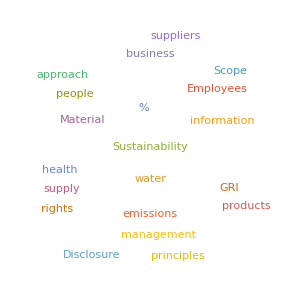
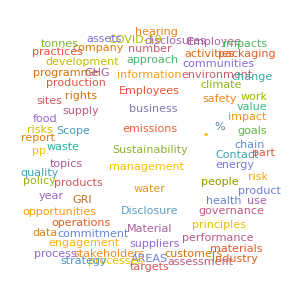
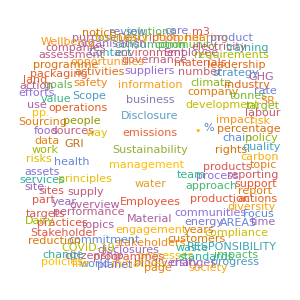

```mathematica
WordCloud[text,MaxItems->#, ImageSize->300, FontFamily->"Helvetica"]&/@select
```

## Binary Classifier

The goal of this section is to construct a binary classifier which takes as input a sentence and classifies it as “SDG” or “non SDG”.

### Training & Test sets Construction

We choose to construct two different classifiers: one trained on sentences from Wikipedia articles and the other trained on sentences from the reports.

#### From Wikipedia

For the first classifier, we select Wikipedia articles that correspond to “SDG” and “non SDG” topics, trying to have balanced classes. These choices are ours and can be subject to modifications and updates.
We then divide each set of sentences in a training set (80%) and a test set (20%).

```mathematica
SDGlist={"Sustainable Development Goals","Sustainability", "Biosphere", "Sustainable development", "Natural environment", "Millennium Development Goals" };
nonSDGlist={"Corporation","Business","Free trade","Economics","List of corporate collapses and scandals","Fossil fuel", "Capital (economics)","Stakeholder (corporate)","Business model"};
SDG=StringTrim[DeleteStopwords[WikipediaData[#,"ArticlePlaintext"]]]&/@SDGlist;//FullForm;
nonSDG=StringTrim[DeleteStopwords[WikipediaData[#,"ArticlePlaintext"]]]&/@nonSDGlist;//FullForm;
```

```mathematica
sentencesSDG=Flatten@TextSentences[SDG];
sentencesNonSDG = Flatten@TextSentences[nonSDG];
```

```mathematica
traintestSDGwiki=ResourceFunction["TrainTestSplit"][sentencesSDG,"Shuffle"->True];
trainingsetSDGwiki=traintestSDGwiki[[1]];
testsetSDGwiki=traintestSDGwiki[[2]];
Print["The size of the training set for 'SDG' class is :"]
Dimensions@trainingsetSDGwiki
Print["The size of the test set for 'SDG' class is :"]
Dimensions@testsetSDGwiki
traintestNonSDGwiki=ResourceFunction["TrainTestSplit"][sentencesNonSDG,"Shuffle"->True];
trainingsetNonSDGwiki=traintestNonSDGwiki[[1]];
testsetNonSDGwiki=traintestNonSDGwiki[[2]];
Print["The size of the training set for 'non SDG' class is :"]
Dimensions@trainingsetNonSDGwiki
Print["The size of the test set for 'non SDG' class is :"]
Dimensions@testsetNonSDGwiki
```

The size of the training set for 'SDG' class is :

{1089}

The size of the test set for 'SDG' class is :

{272}

The size of the training set for 'non SDG' class is :

{1403}

The size of the test set for 'non SDG' class is :

{351}

#### From Reports

For the second classifier, we select sentences that correspond to the “SDG” class in the reports. 
To do so, we use the list of keywords constructed collectively with the other groups, and pick the sentences that contain at least one keyword. 
For the “non SDG” topics we pick the sentences that do not contain any keywords, and then select a random subset to match the size of the ‘SDG’ class (again to have balanced classes). 
We then divide each set of sentences in a training set (80%) and a test set (20%).

```mathematica
tableSDG = Transpose[Import["/Users/jeannefernandez/Desktop/E4S_Master/DataScience/Project/SDG_Keywords_final.xlsx"][[1]]];
keywords = tableSDG[[#]][[2;;331]]&/@Range[17];
keywords = Select[keywords[[#]],UnsameQ[#,""]&]&/@Range[17];
keywordsAssoc = AssociationThread[tableSDG[[#]][[1]]&/@Range[17], keywords];
Flatten@Values@keywordsAssoc;
```

```mathematica
flatKeywords = Flatten@Values@keywordsAssoc;
flatReports = TextSentences@StringJoin@allData2;
Print["The number of keywords is :"]
Dimensions@flatKeywords
Print["The total number of sentences in the reports is :"]
Dimensions@flatReports
```

The number of keywords is :

{230}

The total number of sentences in the reports is :

{80306}

```mathematica
arrayIndices = StringContainsQ[Alternatives@flatKeywords]/@flatReports ;
sentencesSDGreports = Pick[flatReports, arrayIndices];
sentencesNonSDGreports = Pick[flatReports, Map[Not,arrayIndices]];
Print["The number of sentences found related to 'SDG' is :"]
Dimensions@sentencesSDGreports
Print["The number of sentences found related to 'non SDG' is :"]
Dimensions@sentencesNonSDGreports
Print["Hence, the total proportion of sentences 'SDG'/('SDG'+'non SDG') is :"]
N[Dimensions[sentencesSDGreports][[1]]/Dimensions[flatReports][[1]]]
traintestSDGreports=ResourceFunction["TrainTestSplit"][sentencesSDGreports,"Shuffle"->True];
trainingsetSDGreports=traintestSDGreports[[1]];
testsetSDGreports=traintestSDGreports[[2]];
sentencesNonSDGreports = RandomSample[sentencesNonSDGreports,Dimensions[sentencesSDGreports][[1]]];
traintestNonSDGreports=ResourceFunction["TrainTestSplit"][sentencesNonSDGreports,"Shuffle"->True];
trainingsetNonSDGreports=traintestNonSDGreports[[1]];
testsetNonSDGreports=traintestNonSDGreports[[2]];
```

The number of sentences found related to 'SDG' is :

{27807}

The number of sentences found related to 'non SDG' is :

{52499}

Hence, the total proportion of sentences 'SDG'/('SDG'+'non SDG') is :

0.346263

### Dynamic selection of a report & Random selection of sentence

In this subsection, we let the user choose a report from a selected company to randomly pick a sentence from it. This sentence will then be used to illustrate the evaluation of the classifiers.

```mathematica
Companies2 = DeleteDuplicates@Normal@dataRaw[All, "COMPANY"];
```

```mathematica
Column[
{ResourceFunction["DynamicStringSearch"][Companies2,
LabelingFunction->(Button[
Style[#,12],
CopyToClipboard[#],
Appearance->"Palette",##2,
ImageSize->Full]&)],InputField[Dynamic[co],String,FieldHint->"Print your choice using \"CTRL+V\" and click on \"Submit\"",FieldSize->50],Button["Submit",ImageSize->Large]}]
```

Submit

```mathematica
Dynamic@co
```

```mathematica
tmp1 = dataRaw[Select[#COMPANY==co&]]
tmpReports = Normal@tmp1[All,"IDREPORT"];
```

```mathematica
Column[
{ResourceFunction["DynamicStringSearch"][tmpReports,
LabelingFunction->(Button[
Style[#,16],
CopyToClipboard[#],
Appearance->"Palette",##2,
ImageSize->Full]&)],InputField[Dynamic[ro],String,FieldHint->"Print your choice using \"CTRL+V\" and click on \"Submit\"",FieldSize->50],Button["Submit",ImageSize->Large]}]
```

Submit

```mathematica
Dynamic@ro
```

```mathematica
tmp2 = tmp1[Select[ #IDREPORT ==ro &]]
```

```mathematica
report = Import[URL[Normal@tmp2[All, "LINK"][[1]]],"Plaintext"];
reportSentences =  TextSentences[report];
Sentence =reportSentences[[RandomInteger[{1,Dimensions[reportSentences][[1]]}]]]
```

We have set important milestones and intermediate goals for our.02selves along the way: we want to improve the total life-cycle carbon 
footprint of our passenger cars and light commercial vehicles by 
30% compared to 2015 by as early as 2025.

### Select Classifier Method

In this subsection, we let the user choose a method for the classifier.

```mathematica
method={"ClassDistributions","DecisionTree","GradientBoostedTrees","LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"};
```

```mathematica
Column[
{ResourceFunction["DynamicStringSearch"][method,
LabelingFunction->(Button[
Style[#,16],
CopyToClipboard[#],
Appearance->"Palette",##2,
ImageSize->Full]&)],
InputField[Dynamic[me],String,FieldHint->"Print your choice using \"CTRL+V\" and click on \"Submit\"",FieldSize->50],Button["Submit",ImageSize->Large]
}]
```

Submit

```mathematica
list={};
meList=Dynamic@Append[list,me]
```

### Binary Classifier

Now, we construct the two classifiers.

#### Wikipedia classifier

For the first classifier, we use the Wikipedia training and testing sets, and the method previously selected.

```mathematica
classifierList=Classify[<|"SDG"->trainingsetSDGwiki,"Non SDG"->trainingsetNonSDGwiki|>,Method->#]&/@meList;
classifier1=classifierList[[1]];
```

```mathematica
Sentence
classifier1[Sentence, {"TopProbabilities",2}]
```

We have set important milestones and intermediate goals for our.02selves along the way: we want to improve the total life-cycle carbon 
footprint of our passenger cars and light commercial vehicles by 
30% compared to 2015 by as early as 2025.

{SDG→0.648399,Non SDG→0.351601}

```mathematica
DynamicModule[{x=""},Column[{InputField[Dynamic[x],String,FieldHint->"Enter a sentence",FieldSize->70],Dynamic[classifier1[{x},{"TopProbabilities",2}]]}]]
```

Accuracy on training set :

0.986758

Accuracy on test set :

0.916533

Confusion matrix on training set :

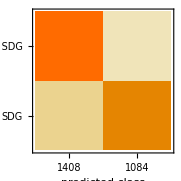

Confusion matrix on test set :

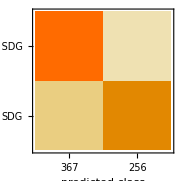

```mathematica
Print["Accuracy on training set : "]
ClassifierMeasurements[classifier1,<|"SDG"->trainingsetSDGwiki,"Non SDG"->trainingsetNonSDGwiki|>,"Accuracy"]
Print["Accuracy on test set : "]
ClassifierMeasurements[classifier1,<|"SDG"->testsetSDGwiki,"Non SDG"->testsetNonSDGwiki|>,"Accuracy"]
Print["Confusion matrix on training set :"]
ClassifierMeasurements[classifier1,<|"SDG"->trainingsetSDGwiki,"Non SDG"->trainingsetNonSDGwiki|>,"ConfusionMatrixPlot"]
Print["Confusion matrix on test set :"]
ClassifierMeasurements[classifier1,<|"SDG"->testsetSDGwiki,"Non SDG"->testsetNonSDGwiki|>,"ConfusionMatrixPlot"]
```

```mathematica
Export["classifier_wiki_1bis.wmlf",classifier1]
```

classifier_wiki_1bis.wmlf

#### Report classifier

For the second classifier, we use the reports for building the training and testing sets, and the method previously selected.

```mathematica
classifier2List=Classify[<|"SDG"->trainingsetSDGreports,"Non SDG"->trainingsetNonSDGreports|>,Method->#]&/@meList;
classifier2=classifier2List[[1]];
```

```mathematica
Sentence
classifier2[Sentence, "TopProbabilities"]
```

We have set important milestones and intermediate goals for our.02selves along the way: we want to improve the total life-cycle carbon 
footprint of our passenger cars and light commercial vehicles by 
30% compared to 2015 by as early as 2025.

{Non SDG→0.882391,SDG→0.117609}

```mathematica
DynamicModule[{x=""},Column[{InputField[Dynamic[x],String,FieldHint->"Enter a sentence",FieldSize->70],Dynamic[classifier2[{x},{"TopProbabilities",2}]]}]]
```

Accuracy on training set:

0.943248

Accuracy on test set:

0.913055

Confusion matrix on training set :

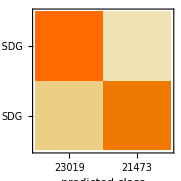

Confusion matrix on test set:

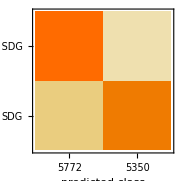

```mathematica
Print["Accuracy on training set: "]
ClassifierMeasurements[classifier2,<|"SDG"->trainingsetSDGreports,"Non SDG"->trainingsetNonSDGreports|>,"Accuracy"]
Print["Accuracy on test set: "]
ClassifierMeasurements[classifier2,<|"SDG"->testsetSDGreports,"Non SDG"->testsetNonSDGreports|>,"Accuracy"]
Print["Confusion matrix on training set :"]
ClassifierMeasurements[classifier2,<|"SDG"->trainingsetSDGreports,"Non SDG"->trainingsetNonSDGreports|>,"ConfusionMatrixPlot"]
Print["Confusion matrix on test set:"]
ClassifierMeasurements[classifier2,<|"SDG"->testsetSDGreports,"Non SDG"->testsetNonSDGreports|>,"ConfusionMatrixPlot"]
```

```mathematica
Export["classifier_report_1bis.wmlf",classifier2]
```

classifier_report_1.wmlf

## Multi-class classifier

In this section, the goal is to construct a multi-class classifier which takes as input a sentence and classifies it between 18 classes : the 17 SDG goals and “non SDG”.

### Training & Test sets Construction

As before, we construct two training and testing sets: one from Wikipedia and one from the reports.

#### From Wikipedia

We use the Wikipedia articles specific for each goals, and the same articles as before for the ‘non SDG’ class, and divide each class into training set (80%) and testing set (20%).

```mathematica
SDGgoalsList = "Sustainable Development Goal "<>ToString[#]&/@Range[17];
SDGgoalsListShort = "SDG "<>ToString[#]&/@Range[17];
SDGgoals=StringTrim[DeleteStopwords[WikipediaData[#,"ArticlePlaintext"]]]&/@SDGgoalsList;//FullForm;
SDGgoalsSentences = TextSentences[SDGgoals];
```

```mathematica
traintestSDGgoalswiki=ResourceFunction["TrainTestSplit"][SDGgoalsSentences[[#]],"Shuffle"->True]&/@Range[17];
trainset3 = traintestSDGgoalswiki[[#,1]]&/@Range[17];
testset3=traintestSDGgoalswiki[[#,2]]&/@Range[17];
```

#### From Reports

For each class, we pick the sentences that contain the keywords of the corresponding SGD goal.

```mathematica
arrayIndices17 = StringContainsQ[flatReports, Alternatives@keywordsAssoc[[#]]] &/@Range[17];
sentencesSDGreports17 = Pick[flatReports, arrayIndices17[[#]]]&/@Range[17];
traintestSDGreports17=ResourceFunction["TrainTestSplit"][sentencesSDGreports17[[#]],"Shuffle"->True]&/@Range[17];
trainset17=traintestSDGreports17[[#,1]]&/@Range[17];
testset17=traintestSDGreports17[[#,2]]&/@Range[17];
```

### Classifier

Now we construct the two classifiers.

#### From Wikipedia

```mathematica
assoTrain = AssociationThread[SDGgoalsListShort, trainset3];
assoTest = AssociationThread[SDGgoalsListShort, testset3];
classifier3List=Classify[<|assoTrain,"Non SDG"->trainingsetNonSDGwiki|>,Method->#]&/@meList;
classifier3=classifier3List[[1]];
```

```mathematica
Sentence
classifier3[Sentence, {"TopProbabilities",3}]
```

We have set important milestones and intermediate goals for our.02selves along the way: we want to improve the total life-cycle carbon 
footprint of our passenger cars and light commercial vehicles by 
30% compared to 2015 by as early as 2025.

{Non SDG→0.171614,SDG 2→0.111581,SDG 9→0.0846273}

```mathematica
DynamicModule[{x=""},Column[{InputField[Dynamic[x],String,FieldHint->"Enter a sentence",FieldSize->70],Dynamic[classifier3[{x},{"TopProbabilities",3}]]}]]
```

Accuracy on training set:

0.866215

Accuracy on test set:

0.742227

Confusion matrix on training set :

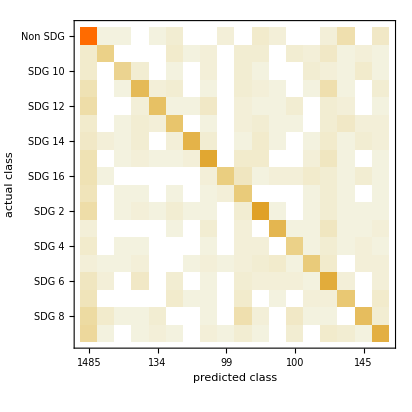

Confusion matrix on test set:

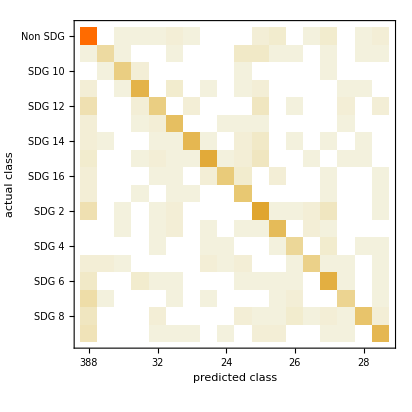

```mathematica
Print["Accuracy on training set: "]
ClassifierMeasurements[classifier3,<|assoTrain,"Non SDG"->trainingsetNonSDGwiki|>,"Accuracy"]
Print["Accuracy on test set: "]
ClassifierMeasurements[classifier3,<|assoTest,"Non SDG"->testsetNonSDGwiki|>,"Accuracy"]
Print["Confusion matrix on training set :"]
ClassifierMeasurements[classifier3,<|assoTrain,"Non SDG"->trainingsetNonSDGwiki|>,"ConfusionMatrixPlot"]
Print["Confusion matrix on test set:"]
ClassifierMeasurements[classifier3,<|assoTest,"Non SDG"->testsetNonSDGwiki|>,"ConfusionMatrixPlot"]
```

```mathematica
Export["classifier_wiki_17bis.wmlf",classifier3]
```

classifier_wiki_17.wmlf

#### From Reports

```mathematica
assoTrain17 = AssociationThread[SDGgoalsListShort, trainset17];
assoTest17 = AssociationThread[SDGgoalsListShort, testset17];
```

```mathematica
classifier4List=Classify[<|assoTrain17,"Non SDG"->trainingsetNonSDGwiki|>,Method->#]&/@meList;
classifier4=classifier4List[[1]];
```

```mathematica
Sentence
classifier4[Sentence, {"TopProbabilities",3}]
```

We have set important milestones and intermediate goals for our.02selves along the way: we want to improve the total life-cycle carbon 
footprint of our passenger cars and light commercial vehicles by 
30% compared to 2015 by as early as 2025.

{SDG 13→0.362845,SDG 7→0.159218,SDG 12→0.06371}

```mathematica
DynamicModule[{x=""},Column[{InputField[Dynamic[x],String,FieldHint->"Enter a sentence",FieldSize->70],Dynamic[classifier4[{x},{"TopProbabilities",3}]]}]]
```

Accuracy on training set:

0.59812

Accuracy on test set:

0.586194

Confusion matrix on training set :

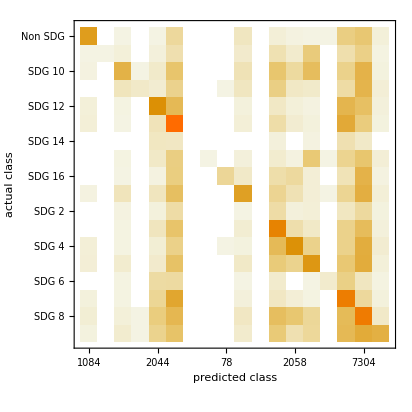

Confusion matrix on test set:

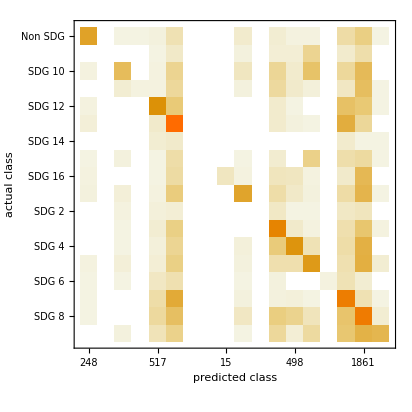

```mathematica
Print["Accuracy on training set: "]
ClassifierMeasurements[classifier4,<|assoTrain17,"Non SDG"->trainingsetNonSDGwiki|>,"Accuracy"]
Print["Accuracy on test set: "]
ClassifierMeasurements[classifier4,<|assoTest17,"Non SDG"->testsetNonSDGwiki|>,"Accuracy"]
Print["Confusion matrix on training set :"]
ClassifierMeasurements[classifier4,<|assoTrain17,"Non SDG"->trainingsetNonSDGwiki|>,"ConfusionMatrixPlot"]
Print["Confusion matrix on test set:"]
ClassifierMeasurements[classifier4,<|assoTest17,"Non SDG"->testsetNonSDGwiki|>,"ConfusionMatrixPlot"]
```

```mathematica
Export["classifier_report_17bis.wmlf",classifier4]
```

classifier_report_17.wmlf